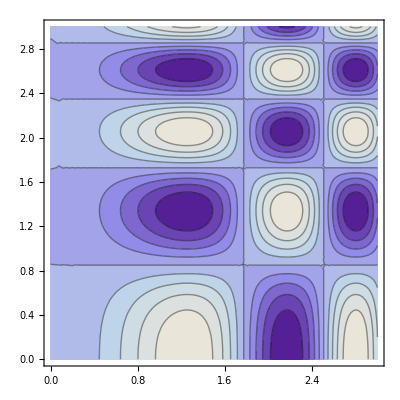

```mathematica
ContourPlot[Sin[x^2]Cos[y^2+y],{x,0,3},{y,0,3}]
```

```mathematica
Manipulate[Plot[{Sin[n x], Cos[n x]}, {x, 0, 2π}], {n, 1, 10}]
```

```mathematica
Manipulate[(a+b+c)^n// Expand, {n, 1, 10, 1}]
```

```mathematica
Manipulate[(a+b+c)^n// Expand, {n, 1, 10, 1}]
```

```mathematica
expr1=1/(x^7+1)
```

1/(1+x^7)

```mathematica
expr2=D[Integrate[expr1,x],x]
```

1/(7 (1+x))-((2 x-2 Cos[π/7]) Cos[π/7])/(7 (1+x^2-2 x Cos[π/7]))+2/(7 (1+(x-Cos[π/7])^2 Csc[π/7]^2))+2/(7 (1+Sec[π/14]^2 (x-Sin[π/14])^2))-((2 x-2 Sin[π/14]) Sin[π/14])/(7 (1+x^2-2 x Sin[π/14]))+(Sin[(3 π)/14] (2 x+2 Sin[(3 π)/14]))/(7 (1+x^2+2 x Sin[(3 π)/14]))+2/(7 (1+Sec[(3 π)/14]^2 (x+Sin[(3 π)/14])^2))

```mathematica
expr2-expr1
```

1/(7 (1+x))-1/(1+x^7)-((2 x-2 Cos[π/7]) Cos[π/7])/(7 (1+x^2-2 x Cos[π/7]))+2/(7 (1+(x-Cos[π/7])^2 Csc[π/7]^2))+2/(7 (1+Sec[π/14]^2 (x-Sin[π/14])^2))-((2 x-2 Sin[π/14]) Sin[π/14])/(7 (1+x^2-2 x Sin[π/14]))+(Sin[(3 π)/14] (2 x+2 Sin[(3 π)/14]))/(7 (1+x^2+2 x Sin[(3 π)/14]))+2/(7 (1+Sec[(3 π)/14]^2 (x+Sin[(3 π)/14])^2))

```mathematica
Together[expr2]
```

(7+6 x+21 x^2+«3363»)/(7 (1+x) (1+x^2-2 x Cos[π/7]) «1»«1»«1» (1+x^2+2 x Sin[(«1»)/14]) (1+x^2 Sec[π/14]^2-2 x Sec[π/14] Tan[π/14]+Tan[π/14]^2) (1+x^2 Sec[(3 π)/14]^2+2 x Sec[(3 π)/14] Tan[(3 π)/14]+Tan[(3 π)/14]^2))

```mathematica
TrigToExp[expr2]
```

1/(7 (1+x))-(ⅈ (ⅇ^(-(ⅈ π)/14)-ⅇ^((ⅈ π)/14)) (-ⅈ (ⅇ^(-(ⅈ π)/14)-ⅇ^((ⅈ π)/14))+2 x))/(14 (1-ⅈ (ⅇ^(-(ⅈ π)/14)-ⅇ^((ⅈ π)/14)) x+x^2))-((ⅇ^(-(ⅈ π)/7)+ⅇ^((ⅈ π)/7)) (-ⅇ^(-(ⅈ π)/7)-ⅇ^((ⅈ π)/7)+2 x))/(14 (1-(ⅇ^(-(ⅈ π)/7)+ⅇ^((ⅈ π)/7)) x+x^2))+(ⅈ (ⅇ^(-(3 ⅈ π)/14)-ⅇ^((3 ⅈ π)/14)) (ⅈ (ⅇ^(-(3 ⅈ π)/14)-ⅇ^((3 ⅈ π)/14))+2 x))/(14 (1+ⅈ (ⅇ^(-(3 ⅈ π)/14)-ⅇ^((3 ⅈ π)/14)) x+x^2))+2/(7 (1+(4 (-1/2 ⅈ (ⅇ^(-(ⅈ π)/14)-ⅇ^((ⅈ π)/14))+x)^2)/((ⅇ^(-(ⅈ π)/14)+ⅇ^((ⅈ π)/14))^2)))+2/(7 (1-(4 (1/2 (-ⅇ^(-(ⅈ π)/7)-ⅇ^((ⅈ π)/7))+x)^2)/((ⅇ^(-(ⅈ π)/7)-ⅇ^((ⅈ π)/7))^2)))+2/(7 (1+(4 (1/2 ⅈ (ⅇ^(-(3 ⅈ π)/14)-ⅇ^((3 ⅈ π)/14))+x)^2)/((ⅇ^(-(3 ⅈ π)/14)+ⅇ^((3 ⅈ π)/14))^2)))

```mathematica
TrigToExp[{expr1, expr2}]
```

{1/(1+x^7),1/(7 (1+x))-(ⅈ (ⅇ^(-(ⅈ π)/14)-ⅇ^((ⅈ π)/14)) (-ⅈ (ⅇ^(-(ⅈ π)/14)-ⅇ^((ⅈ π)/14))+2 x))/(14 (1-ⅈ (ⅇ^(-(ⅈ π)/14)-ⅇ^((ⅈ π)/14)) x+x^2))-((ⅇ^(-(ⅈ π)/7)+ⅇ^((ⅈ π)/7)) (-ⅇ^(-(ⅈ π)/7)-ⅇ^((ⅈ π)/7)+2 x))/(14 (1-(ⅇ^(-(ⅈ π)/7)+ⅇ^((ⅈ π)/7)) x+x^2))+(ⅈ (ⅇ^(-(3 ⅈ π)/14)-ⅇ^((3 ⅈ π)/14)) (ⅈ (ⅇ^(-(3 ⅈ π)/14)-ⅇ^((3 ⅈ π)/14))+2 x))/(14 (1+ⅈ (ⅇ^(-(3 ⅈ π)/14)-ⅇ^((3 ⅈ π)/14)) x+x^2))+2/(7 (1+(4 (-1/2 ⅈ (ⅇ^(-(ⅈ π)/14)-ⅇ^((ⅈ π)/14))+x)^2)/((ⅇ^(-(ⅈ π)/14)+ⅇ^((ⅈ π)/14))^2)))+2/(7 (1-(4 (1/2 (-ⅇ^(-(ⅈ π)/7)-ⅇ^((ⅈ π)/7))+x)^2)/((ⅇ^(-(ⅈ π)/7)-ⅇ^((ⅈ π)/7))^2)))+2/(7 (1+(4 (1/2 ⅈ (ⅇ^(-(3 ⅈ π)/14)-ⅇ^((3 ⅈ π)/14))+x)^2)/((ⅇ^(-(3 ⅈ π)/14)+ⅇ^((3 ⅈ π)/14))^2)))}

```mathematica
Simplify[expr1/expr2]
```

$Aborted

```mathematica
Simplify[expr2-expr1]
```

0